Question 1 
The electric potential in a region of space is given by V=100(x^2-y^2) in volts, where x and y are in meters.
a)       Draw a contour map of the potential, showing and labeling the -400 V, -100 V, 0 V, +100 V , and +400 V equipotential surfaces.
b)        Find an expression for the electric field E⃗ at position (x,y).
	E = -dV = -d(100(x^2-y^2)) = 100 * -(2x - 2y) = 200y-200x
c)	Draw the electric field lines on your diagram of part a.

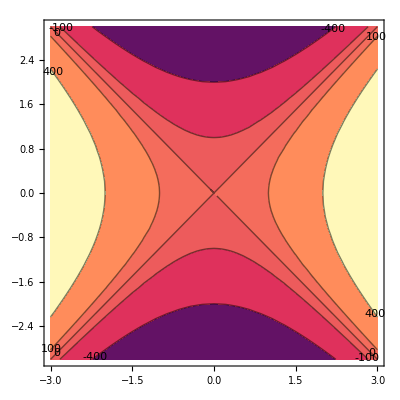

```mathematica
V[x_,y_]:=100(x^2-y^2);
ContourPlot[V[x,y],{x,-3,3},{y,-3,3},Contours->{-400,-100,0,100,400} ,ContourLabels->True]
```

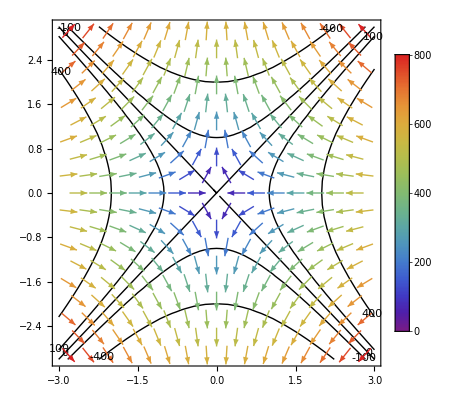

```mathematica
V[x_,y_]:=100(x^2-y^2);
Ex[x_]:=-200x;
Ey[y_]:=200y;
as=VectorPlot[{Ex[x],Ey[y]},{x,-3,3},{y,-3,3},VectorColorFunction->"Rainbow",PlotLegends->Automatic];
cs=ContourPlot[V[x,y],{x,-3,3},{y,-3,3},Contours->{-400,-100,0,100,400} ,ContourLabels->True,ContourShading->None];
Show[cs,as]
```

Question 2
Charge is uniformly distributed with a density of 100.0 μC/m3 throughout the volume of a cube 10.00 cm on each edge.
a)	 Find the electric potential at a distance of 5.000 cm from the center of one face of the cube, measured along a perpendicular to the face. Determine the potential to four significant figures. Use a numerical method that divides the cube into a sufficient number of smaller cubes, treated as point charges.  (Note:  use a value of k = 8.98755 x 109 N m2/C2)
	kq / r
b)	If the charge in the cube is redistributed into a uniform sphere of charge with the same center, by how much does the potential change?

```mathematica
coulombsConstant=8.98755*10^9;
xp=.1;
rho=100*10^-6;
L=.1;
n=20;
dl=L/n;
Vol=dl^3;
dq=rho*Vol;
start=-L/2 + dl/2;
r[x_,y_,z_,xp_]:=Sqrt[(x-xp)^2+y^2+z^2];
V[r_]:=coulombsConstant * dq /r;
Vp=0;
For[k=1,k<=n,k=k+1,
For[i=1,i<=n,i=i+1,
For[j=1,j<=n,j=j+1,
x=start+(i-1)*dl;
y=start+(j-1)*dl;;
z=start+(k-1)*dl;;
dist=r[x,y,z,xp];
Vp=Vp+V[dist];
]
]
];
Vp
Vpt=coulombsConstant * (rho * L^3)/xp
```

8876.04

8987.55

Question 31.	It is postulated that the radial electric field of a group of charges falls off as  Er = C/r^n, where C is a constant, r is the distance from the center of the group, and n is an unknown exponent. To test this hypothesis, you make a field probe consisting of two needle tips spaced 1.00 mm apart. You orient the needles so that a line between the tips points to the center of the charges, then use a voltmeter to read the potential difference between the tips. After you take measurements at several distances from the center of the group, your data are as follows: 2.0, 4.0, 6.0, 8.0, 10.0 cm with 34.7, 6.6, 2.1, 1.2, 0.6, mV respectively. Use an appropriate graph of the data to determine the constants C and n. Include your graph.

Clear::wrsym: Symbol C is Protected.

{C→0.00251933,n→2.43631}

Function[{r},0.00251933/r^2.43631]

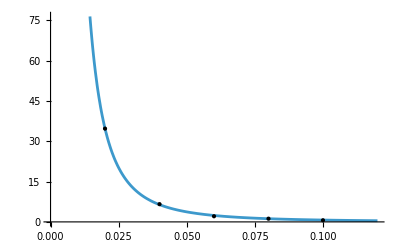

```mathematica
Clear[C,n,r]
distance=Table[x*0.02,{x,5}];
Efield=Table[0,5];
Efield[[1]]=34.7;
Efield[[2]]=6.6;
Efield[[3]]=2.1;
Efield[[4]]=1.2;
Efield[[5]]=0.6;

data=Thread[{distance,Efield}];
model=C/r^n;
fit=FindFit[data,model,{C,n},r]
modelf=Function[{r},Evaluate[model/.fit]]
Plot[modelf[r],{r,0,.12},Epilog->Map[Point,data]]
```